## Introduction

Stuff here

## Main

## States

### Vary σ

```mathematica
plotLocal[z_,L_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text["d = 1",{2.5,2.5}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->15];
Return[p1];
];

run[d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff},
{dt,T,n}={0.25,100,50};
{J,k}={1,1};
{R,L,Ω}={1,4,1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
Return[znew];
];
```

```mathematica
d=0;
σs=Table[σ,{σ,0.5,3,0.5}];
dataZσ=ParallelTable[run[d,σ],{σ,σs}];
```

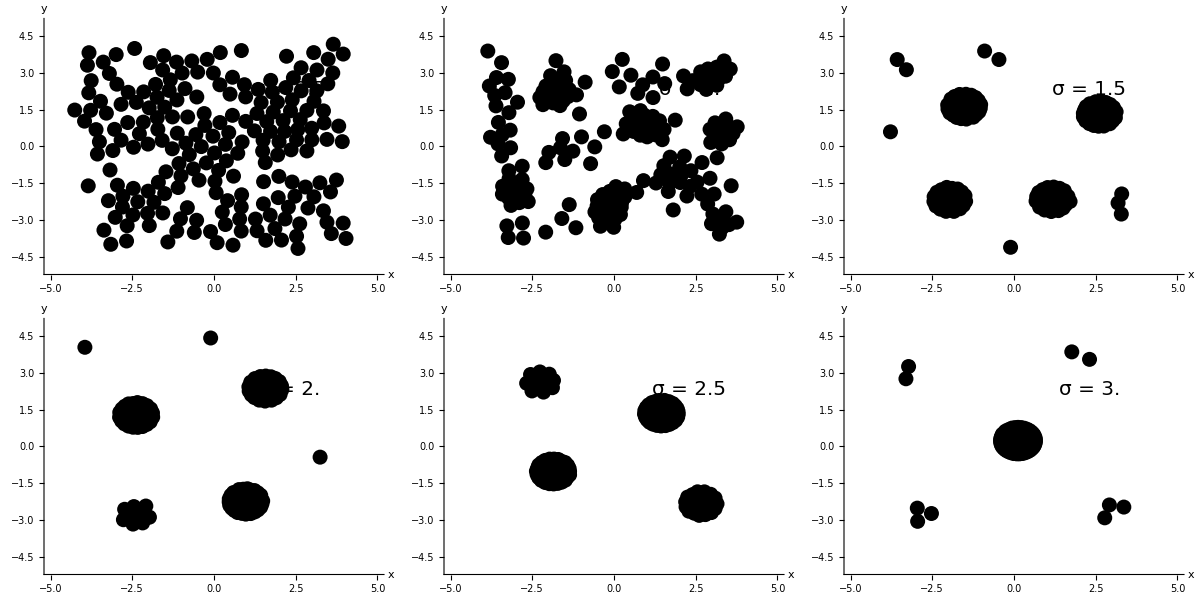

```mathematica
plotLocal[z_,L_,σ_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text[Style["σ = "<>ToString[σ],20],{2.3,2.3}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->19];
Return[p1];
];
plots=Table[plotLocal[dataZσ[[i]],5,σs[[i]]],{i,1,Length[σs]}];
p1=Grid[Partition[plots,3]]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-states-different-σ.png",p1];
```

#### Paper plot

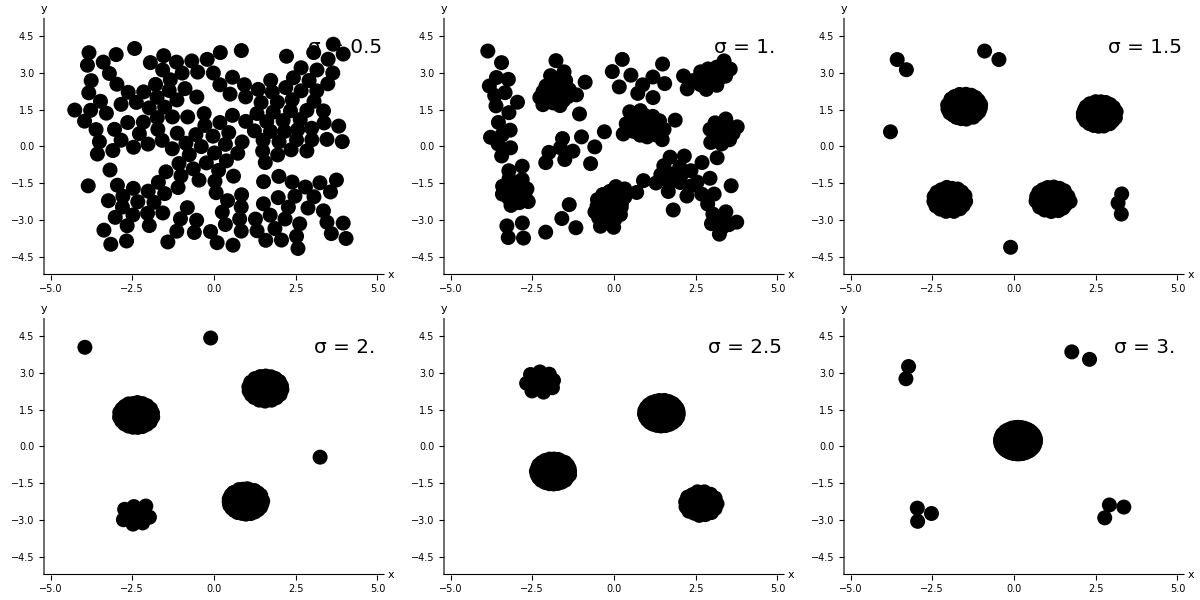

```mathematica
plotLocal[z_,L_,σ_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text[Style["σ = "<>ToString[σ],20],{4,4}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->19];
Return[p1];
];
plots=Table[plotLocal[dataZσ[[i]],5,σs[[i]]],{i,1,Length[σs]}];
p1=Grid[Partition[plots,3]]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-states-different-σ.png",p1];
```

#### Change d

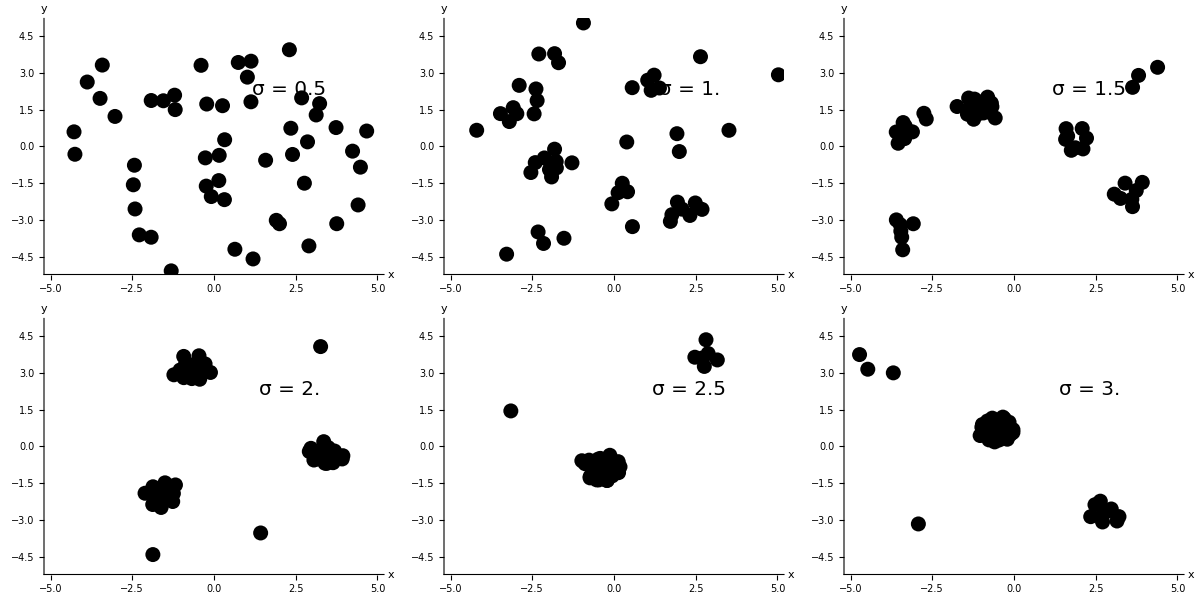

```mathematica
run[d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff},
{dt,T,n}={0.25,100,50};
{J,k}={1,1};
{R,L,Ω}={1,4,1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
Return[znew];
];

d=0.1;
σs=Table[σ,{σ,0.5,3,0.5}];
dataZσ=ParallelTable[run[d,σ],{σ,σs}];
plotLocal[z_,L_,σ_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text[Style["σ = "<>ToString[σ],20],{2.3,2.3}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->19];
Return[p1];
];
plots=Table[plotLocal[dataZσ[[i]],5,σs[[i]]],{i,1,Length[σs]}];
p1=Grid[Partition[plots,3]]
SetDirectory[NotebookDirectory[]];
(*Export["figures/sync-states-different-σ.png",p1];*)
```

## G(r)

### Method

```mathematica
run[d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff,x,y,θ,xs,ys,θs},
{dt,T,n}={0.25,200,500};
{J,k}={1,1};
{R,L,Ω}={1,4,1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];{x,y,θ}=znew;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
Return[{xs,ys,θs}];
];

findg[xs_,ys_,θs_,t_,n_]:=Block[{rijs,min,max,dr,binnedData,g},
rijs=findRijNij[xs,ys,θs,t,n][[All,1]];
{min,max,dr}={0,12,0.05};
r=Table[i,{i,min,max,dr}];
r=Table[(r[[i]]+r[[i+1]])/2,{i,1,Length[r]-1}];
binnedData=BinLists[rijs,{min,max,dr}];
g=N[Table[Length[binnedData[[i]]],{i,1,Length[binnedData]}]/(n(n-1))];
Return[{r,g}ᵀ];
];
```

### Plot

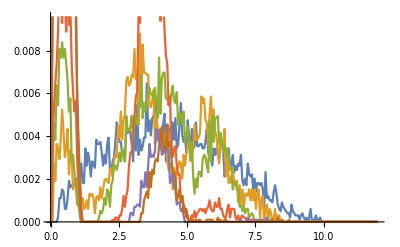

```mathematica
{d,σ}={0,4};
σs=Table[σ,{σ,0.5,3,0.5}];
allData={};
gdata=ParallelTable[{x,y,θ}=run[d,σ];AppendTo[allData,{x,y,θ}];findg[x,y,θ,t,n],{σ,σs}];
ListPlot[gdata,Joined->True]
```

#### Data paper

```mathematica
gdata={{{0.025,0.},{0.07500000000000001,0.},{0.125,0.},{0.17500000000000002,0.},{0.225,0.},{0.275,0.00020202020202020202},{0.32500000000000007,0.0011111111111111111},{0.375,0.0011111111111111111},{0.42500000000000004,0.0015151515151515152},{0.475,0.0014141414141414141},{0.525,0.0006060606060606061},{0.5750000000000001,0.0006060606060606061},{0.625,0.0011111111111111111},{0.675,0.0019191919191919192},{0.7250000000000001,0.0016161616161616162},{0.775,0.0017171717171717172},{0.8250000000000001,0.0016161616161616162},{0.875,0.0018181818181818182},{0.925,0.00202020202020202},{0.9750000000000001,0.0012121212121212121},{1.025,0.0013131313131313131},{1.0750000000000002,0.0026262626262626263},{1.125,0.0027272727272727275},{1.1750000000000003,0.0018181818181818182},{1.225,0.0018181818181818182},{1.275,0.0034343434343434343},{1.3250000000000002,0.0026262626262626263},{1.375,0.0032323232323232323},{1.4250000000000003,0.0028282828282828283},{1.475,0.0021212121212121214},{1.525,0.0028282828282828283},{1.5750000000000002,0.0027272727272727275},{1.625,0.0025252525252525255},{1.6750000000000003,0.0038383838383838384},{1.725,0.0036363636363636364},{1.775,0.0036363636363636364},{1.8250000000000002,0.0037373737373737376},{1.875,0.0032323232323232323},{1.9250000000000003,0.0026262626262626263},{1.975,0.0031313131313131315},{2.0250000000000004,0.0027272727272727275},{2.075,0.0036363636363636364},{2.125,0.00393939393939394},{2.175,0.0024242424242424242},{2.225,0.0023232323232323234},{2.2750000000000004,0.0028282828282828283},{2.325,0.0030303030303030303},{2.375,0.0037373737373737376},{2.4250000000000003,0.004646464646464647},{2.475,0.004242424242424243},{2.5250000000000004,0.0037373737373737376},{2.575,0.0037373737373737376},{2.625,0.0031313131313131315},{2.6750000000000003,0.0033333333333333335},{2.725,0.0028282828282828283},{2.7750000000000004,0.004646464646464647},{2.825,0.004141414141414141},{2.875,0.004343434343434344},{2.9250000000000003,0.004141414141414141},{2.975,0.0036363636363636364},{3.0250000000000004,0.0028282828282828283},{3.075,0.004949494949494949},{3.125,0.0033333333333333335},{3.1750000000000003,0.005454545454545455},{3.225,0.0031313131313131315},{3.2750000000000004,0.0038383838383838384},{3.325,0.0033333333333333335},{3.375,0.0035353535353535356},{3.4250000000000003,0.00393939393939394},{3.475,0.00393939393939394},{3.5250000000000004,0.006464646464646465},{3.575,0.004242424242424243},{3.625,0.004747474747474748},{3.6750000000000003,0.00404040404040404},{3.725,0.0048484848484848485},{3.7750000000000004,0.004949494949494949},{3.825,0.005757575757575757},{3.875,0.00404040404040404},{3.9250000000000003,0.004141414141414141},{3.975,0.0037373737373737376},{4.025,0.0036363636363636364},{4.075,0.0033333333333333335},{4.125,0.004545454545454545},{4.175000000000001,0.005050505050505051},{4.225,0.0028282828282828283},{4.275,0.004545454545454545},{4.325,0.004343434343434344},{4.375,0.004343434343434344},{4.425000000000001,0.0035353535353535356},{4.475,0.004646464646464647},{4.525,0.0038383838383838384},{4.575,0.0048484848484848485},{4.625,0.0034343434343434343},{4.675000000000001,0.0036363636363636364},{4.725,0.004545454545454545},{4.775,0.005555555555555556},{4.825000000000001,0.00404040404040404},{4.875,0.0037373737373737376},{4.925000000000001,0.00404040404040404},{4.975,0.0032323232323232323},{5.025,0.004747474747474748},{5.075000000000001,0.00404040404040404},{5.125,0.0030303030303030303},{5.175000000000001,0.004343434343434344},{5.225,0.0034343434343434343},{5.275,0.0035353535353535356},{5.325000000000001,0.004646464646464647},{5.375,0.0035353535353535356},{5.425000000000001,0.0035353535353535356},{5.475,0.0036363636363636364},{5.525,0.0036363636363636364},{5.575000000000001,0.0034343434343434343},{5.625,0.0034343434343434343},{5.675000000000001,0.0037373737373737376},{5.725,0.004343434343434344},{5.775,0.0032323232323232323},{5.825000000000001,0.0032323232323232323},{5.875,0.0031313131313131315},{5.925000000000001,0.0026262626262626263},{5.975,0.0034343434343434343},{6.025,0.0031313131313131315},{6.075000000000001,0.0034343434343434343},{6.125,0.0031313131313131315},{6.175000000000001,0.0029292929292929295},{6.225,0.0036363636363636364},{6.275,0.0038383838383838384},{6.325000000000001,0.0033333333333333335},{6.375,0.0021212121212121214},{6.425000000000001,0.0026262626262626263},{6.475,0.0029292929292929295},{6.525,0.0034343434343434343},{6.575000000000001,0.0026262626262626263},{6.625,0.0026262626262626263},{6.675000000000001,0.0031313131313131315},{6.725,0.0023232323232323234},{6.775,0.0026262626262626263},{6.825000000000001,0.0024242424242424242},{6.875,0.0027272727272727275},{6.925000000000001,0.0026262626262626263},{6.975,0.0031313131313131315},{7.025,0.0019191919191919192},{7.075000000000001,0.0017171717171717172},{7.125,0.00202020202020202},{7.175000000000001,0.0017171717171717172},{7.225,0.0027272727272727275},{7.275,0.0022222222222222222},{7.325000000000001,0.0021212121212121214},{7.375,0.0022222222222222222},{7.425000000000001,0.0015151515151515152},{7.475,0.00202020202020202},{7.525,0.0014141414141414141},{7.575000000000001,0.0018181818181818182},{7.625,0.0018181818181818182},{7.675000000000001,0.0017171717171717172},{7.725,0.0018181818181818182},{7.775,0.0015151515151515152},{7.825000000000001,0.0007070707070707071},{7.875,0.0023232323232323234},{7.925000000000001,0.0011111111111111111},{7.975,0.0012121212121212121},{8.025,0.00101010101010101},{8.075,0.00101010101010101},{8.125,0.0009090909090909091},{8.175,0.0014141414141414141},{8.225000000000001,0.0017171717171717172},{8.275,0.0013131313131313131},{8.325,0.0008080808080808081},{8.375,0.0006060606060606061},{8.425,0.000505050505050505},{8.475000000000001,0.0009090909090909091},{8.525,0.0007070707070707071},{8.575,0.0006060606060606061},{8.625,0.000505050505050505},{8.675,0.00040404040404040404},{8.725000000000001,0.00040404040404040404},{8.775,0.00020202020202020202},{8.825,0.0008080808080808081},{8.875,0.000505050505050505},{8.925,0.00040404040404040404},{8.975000000000001,0.00030303030303030303},{9.025,0.00030303030303030303},{9.075,0.00030303030303030303},{9.125,0.00010101010101010101},{9.175,0.00030303030303030303},{9.225000000000001,0.00040404040404040404},{9.275,0.00020202020202020202},{9.325,0.00010101010101010101},{9.375,0.00020202020202020202},{9.425,0.},{9.475000000000001,0.00020202020202020202},{9.525,0.0006060606060606061},{9.575000000000001,0.},{9.625,0.00010101010101010101},{9.675,0.00010101010101010101},{9.725000000000001,0.00030303030303030303},{9.775,0.},{9.825000000000001,0.00010101010101010101},{9.875,0.00020202020202020202},{9.925,0.},{9.975000000000001,0.},{10.025,0.},{10.075000000000001,0.},{10.125,0.},{10.175,0.},{10.225000000000001,0.},{10.275,0.},{10.325000000000001,0.},{10.375,0.},{10.425,0.},{10.475000000000001,0.},{10.525,0.},{10.575000000000001,0.},{10.625,0.},{10.675,0.},{10.725000000000001,0.},{10.775,0.},{10.825000000000001,0.},{10.875,0.},{10.925,0.},{10.975000000000001,0.},{11.025,0.},{11.075000000000001,0.},{11.125,0.},{11.175,0.},{11.225000000000001,0.},{11.275,0.},{11.325000000000001,0.},{11.375,0.},{11.425,0.},{11.475000000000001,0.},{11.525,0.},{11.575000000000001,0.},{11.625,0.},{11.675,0.},{11.725000000000001,0.},{11.775,0.},{11.825000000000001,0.},{11.875,0.},{11.925,0.},{11.975000000000001,0.}},{{0.025,0.},{0.07500000000000001,0.},{0.125,0.0027272727272727275},{0.17500000000000002,0.0019191919191919192},{0.225,0.0036363636363636364},{0.275,0.0034343434343434343},{0.32500000000000007,0.0029292929292929295},{0.375,0.00393939393939394},{0.42500000000000004,0.0052525252525252525},{0.475,0.004242424242424243},{0.525,0.0030303030303030303},{0.5750000000000001,0.0034343434343434343},{0.625,0.004343434343434344},{0.675,0.0022222222222222222},{0.7250000000000001,0.0033333333333333335},{0.775,0.0030303030303030303},{0.8250000000000001,0.0015151515151515152},{0.875,0.0019191919191919192},{0.925,0.0019191919191919192},{0.9750000000000001,0.0014141414141414141},{1.025,0.0007070707070707071},{1.0750000000000002,0.0009090909090909091},{1.125,0.00101010101010101},{1.1750000000000003,0.0011111111111111111},{1.225,0.0006060606060606061},{1.275,0.0007070707070707071},{1.3250000000000002,0.00101010101010101},{1.375,0.0006060606060606061},{1.4250000000000003,0.0013131313131313131},{1.475,0.0012121212121212121},{1.525,0.0013131313131313131},{1.5750000000000002,0.0011111111111111111},{1.625,0.00040404040404040404},{1.6750000000000003,0.0011111111111111111},{1.725,0.0012121212121212121},{1.775,0.00101010101010101},{1.8250000000000002,0.0016161616161616162},{1.875,0.0011111111111111111},{1.9250000000000003,0.0015151515151515152},{1.975,0.0019191919191919192},{2.0250000000000004,0.00202020202020202},{2.075,0.0019191919191919192},{2.125,0.0018181818181818182},{2.175,0.0024242424242424242},{2.225,0.0025252525252525255},{2.2750000000000004,0.0021212121212121214},{2.325,0.0028282828282828283},{2.375,0.0031313131313131315},{2.4250000000000003,0.0030303030303030303},{2.475,0.0044444444444444444},{2.5250000000000004,0.00393939393939394},{2.575,0.005151515151515152},{2.625,0.0038383838383838384},{2.6750000000000003,0.004747474747474748},{2.725,0.005050505050505051},{2.7750000000000004,0.0065656565656565654},{2.825,0.006767676767676768},{2.875,0.006363636363636364},{2.9250000000000003,0.006464646464646465},{2.975,0.006868686868686869},{3.0250000000000004,0.006767676767676768},{3.075,0.00808080808080808},{3.125,0.006666666666666667},{3.1750000000000003,0.006868686868686869},{3.225,0.004545454545454545},{3.2750000000000004,0.008787878787878787},{3.325,0.0056565656565656566},{3.375,0.008282828282828282},{3.4250000000000003,0.0069696969696969695},{3.475,0.0069696969696969695},{3.5250000000000004,0.006868686868686869},{3.575,0.006868686868686869},{3.625,0.005454545454545455},{3.6750000000000003,0.005353535353535353},{3.725,0.0056565656565656566},{3.7750000000000004,0.006161616161616161},{3.825,0.0036363636363636364},{3.875,0.005050505050505051},{3.9250000000000003,0.004343434343434344},{3.975,0.00393939393939394},{4.025,0.0038383838383838384},{4.075,0.00393939393939394},{4.125,0.0033333333333333335},{4.175000000000001,0.0032323232323232323},{4.225,0.004242424242424243},{4.275,0.0028282828282828283},{4.325,0.0024242424242424242},{4.375,0.0027272727272727275},{4.425000000000001,0.0026262626262626263},{4.475,0.0015151515151515152},{4.525,0.0025252525252525255},{4.575,0.0016161616161616162},{4.625,0.0025252525252525255},{4.675000000000001,0.0025252525252525255},{4.725,0.0028282828282828283},{4.775,0.0027272727272727275},{4.825000000000001,0.00202020202020202},{4.875,0.0031313131313131315},{4.925000000000001,0.0026262626262626263},{4.975,0.0031313131313131315},{5.025,0.0036363636363636364},{5.075000000000001,0.0038383838383838384},{5.125,0.0028282828282828283},{5.175000000000001,0.0029292929292929295},{5.225,0.0034343434343434343},{5.275,0.004545454545454545},{5.325000000000001,0.0038383838383838384},{5.375,0.0038383838383838384},{5.425000000000001,0.00393939393939394},{5.475,0.004141414141414141},{5.525,0.005858585858585859},{5.575000000000001,0.005555555555555556},{5.625,0.005757575757575757},{5.675000000000001,0.004747474747474748},{5.725,0.004646464646464647},{5.775,0.0035353535353535356},{5.825000000000001,0.005050505050505051},{5.875,0.005858585858585859},{5.925000000000001,0.004545454545454545},{5.975,0.0052525252525252525},{6.025,0.004242424242424243},{6.075000000000001,0.00404040404040404},{6.125,0.0032323232323232323},{6.175000000000001,0.0027272727272727275},{6.225,0.004141414141414141},{6.275,0.0038383838383838384},{6.325000000000001,0.0034343434343434343},{6.375,0.004343434343434344},{6.425000000000001,0.0021212121212121214},{6.475,0.0034343434343434343},{6.525,0.0018181818181818182},{6.575000000000001,0.0021212121212121214},{6.625,0.0018181818181818182},{6.675000000000001,0.0025252525252525255},{6.725,0.0018181818181818182},{6.775,0.0019191919191919192},{6.825000000000001,0.0019191919191919192},{6.875,0.0009090909090909091},{6.925000000000001,0.0017171717171717172},{6.975,0.0009090909090909091},{7.025,0.0015151515151515152},{7.075000000000001,0.000505050505050505},{7.125,0.0013131313131313131},{7.175000000000001,0.0013131313131313131},{7.225,0.0012121212121212121},{7.275,0.0015151515151515152},{7.325000000000001,0.00101010101010101},{7.375,0.0015151515151515152},{7.425000000000001,0.00101010101010101},{7.475,0.0015151515151515152},{7.525,0.0006060606060606061},{7.575000000000001,0.0013131313131313131},{7.625,0.0015151515151515152},{7.675000000000001,0.00020202020202020202},{7.725,0.00101010101010101},{7.775,0.0012121212121212121},{7.825000000000001,0.},{7.875,0.0006060606060606061},{7.925000000000001,0.0008080808080808081},{7.975,0.},{8.025,0.0006060606060606061},{8.075,0.00040404040404040404},{8.125,0.00010101010101010101},{8.175,0.00010101010101010101},{8.225000000000001,0.0006060606060606061},{8.275,0.},{8.325,0.00030303030303030303},{8.375,0.00030303030303030303},{8.425,0.},{8.475000000000001,0.},{8.525,0.},{8.575,0.},{8.625,0.},{8.675,0.},{8.725000000000001,0.},{8.775,0.},{8.825,0.},{8.875,0.},{8.925,0.},{8.975000000000001,0.},{9.025,0.},{9.075,0.},{9.125,0.},{9.175,0.},{9.225000000000001,0.},{9.275,0.},{9.325,0.},{9.375,0.},{9.425,0.},{9.475000000000001,0.},{9.525,0.},{9.575000000000001,0.},{9.625,0.},{9.675,0.},{9.725000000000001,0.},{9.775,0.},{9.825000000000001,0.},{9.875,0.},{9.925,0.},{9.975000000000001,0.},{10.025,0.},{10.075000000000001,0.},{10.125,0.},{10.175,0.},{10.225000000000001,0.},{10.275,0.},{10.325000000000001,0.},{10.375,0.},{10.425,0.},{10.475000000000001,0.},{10.525,0.},{10.575000000000001,0.},{10.625,0.},{10.675,0.},{10.725000000000001,0.},{10.775,0.},{10.825000000000001,0.},{10.875,0.},{10.925,0.},{10.975000000000001,0.},{11.025,0.},{11.075000000000001,0.},{11.125,0.},{11.175,0.},{11.225000000000001,0.},{11.275,0.},{11.325000000000001,0.},{11.375,0.},{11.425,0.},{11.475000000000001,0.},{11.525,0.},{11.575000000000001,0.},{11.625,0.},{11.675,0.},{11.725000000000001,0.},{11.775,0.},{11.825000000000001,0.},{11.875,0.},{11.925,0.},{11.975000000000001,0.}},{{0.025,0.},{0.07500000000000001,0.0018181818181818182},{0.125,0.004646464646464647},{0.17500000000000002,0.0038383838383838384},{0.225,0.006363636363636364},{0.275,0.005454545454545455},{0.32500000000000007,0.00808080808080808},{0.375,0.007676767676767677},{0.42500000000000004,0.008383838383838384},{0.475,0.007676767676767677},{0.525,0.00808080808080808},{0.5750000000000001,0.0073737373737373735},{0.625,0.0065656565656565654},{0.675,0.005151515151515152},{0.7250000000000001,0.005757575757575757},{0.775,0.0028282828282828283},{0.8250000000000001,0.0031313131313131315},{0.875,0.0023232323232323234},{0.925,0.0017171717171717172},{0.9750000000000001,0.0008080808080808081},{1.025,0.0009090909090909091},{1.0750000000000002,0.00020202020202020202},{1.125,0.},{1.1750000000000003,0.},{1.225,0.},{1.275,0.},{1.3250000000000002,0.},{1.375,0.},{1.4250000000000003,0.},{1.475,0.},{1.525,0.},{1.5750000000000002,0.},{1.625,0.},{1.6750000000000003,0.},{1.725,0.},{1.775,0.00020202020202020202},{1.8250000000000002,0.000505050505050505},{1.875,0.00040404040404040404},{1.9250000000000003,0.0006060606060606061},{1.975,0.0011111111111111111},{2.0250000000000004,0.0008080808080808081},{2.075,0.0015151515151515152},{2.125,0.0014141414141414141},{2.175,0.0007070707070707071},{2.225,0.0017171717171717172},{2.2750000000000004,0.0019191919191919192},{2.325,0.0026262626262626263},{2.375,0.0026262626262626263},{2.4250000000000003,0.0024242424242424242},{2.475,0.0027272727272727275},{2.5250000000000004,0.0032323232323232323},{2.575,0.0028282828282828283},{2.625,0.0034343434343434343},{2.6750000000000003,0.0030303030303030303},{2.725,0.0028282828282828283},{2.7750000000000004,0.004949494949494949},{2.825,0.004242424242424243},{2.875,0.004242424242424243},{2.9250000000000003,0.0044444444444444444},{2.975,0.004949494949494949},{3.0250000000000004,0.0038383838383838384},{3.075,0.0048484848484848485},{3.125,0.0048484848484848485},{3.1750000000000003,0.004545454545454545},{3.225,0.005555555555555556},{3.2750000000000004,0.005353535353535353},{3.325,0.006868686868686869},{3.375,0.0048484848484848485},{3.4250000000000003,0.005555555555555556},{3.475,0.005151515151515152},{3.5250000000000004,0.005555555555555556},{3.575,0.006262626262626263},{3.625,0.006262626262626263},{3.6750000000000003,0.00595959595959596},{3.725,0.00595959595959596},{3.7750000000000004,0.005757575757575757},{3.825,0.006262626262626263},{3.875,0.005555555555555556},{3.9250000000000003,0.0048484848484848485},{3.975,0.007676767676767677},{4.025,0.005050505050505051},{4.075,0.006666666666666667},{4.125,0.0069696969696969695},{4.175000000000001,0.0069696969696969695},{4.225,0.005757575757575757},{4.275,0.005757575757575757},{4.325,0.005555555555555556},{4.375,0.005454545454545455},{4.425000000000001,0.00595959595959596},{4.475,0.006363636363636364},{4.525,0.0056565656565656566},{4.575,0.005555555555555556},{4.625,0.006060606060606061},{4.675000000000001,0.004545454545454545},{4.725,0.005050505050505051},{4.775,0.005050505050505051},{4.825000000000001,0.004545454545454545},{4.875,0.005151515151515152},{4.925000000000001,0.0037373737373737376},{4.975,0.00404040404040404},{5.025,0.0044444444444444444},{5.075000000000001,0.0037373737373737376},{5.125,0.0029292929292929295},{5.175000000000001,0.0037373737373737376},{5.225,0.0021212121212121214},{5.275,0.0013131313131313131},{5.325000000000001,0.00202020202020202},{5.375,0.0016161616161616162},{5.425000000000001,0.0023232323232323234},{5.475,0.0023232323232323234},{5.525,0.0021212121212121214},{5.575000000000001,0.0029292929292929295},{5.625,0.0031313131313131315},{5.675000000000001,0.0030303030303030303},{5.725,0.0026262626262626263},{5.775,0.0023232323232323234},{5.825000000000001,0.004747474747474748},{5.875,0.0028282828282828283},{5.925000000000001,0.004949494949494949},{5.975,0.0037373737373737376},{6.025,0.0048484848484848485},{6.075000000000001,0.0048484848484848485},{6.125,0.004949494949494949},{6.175000000000001,0.0036363636363636364},{6.225,0.004141414141414141},{6.275,0.0036363636363636364},{6.325000000000001,0.0032323232323232323},{6.375,0.0036363636363636364},{6.425000000000001,0.0033333333333333335},{6.475,0.0030303030303030303},{6.525,0.0031313131313131315},{6.575000000000001,0.0024242424242424242},{6.625,0.0025252525252525255},{6.675000000000001,0.0015151515151515152},{6.725,0.0018181818181818182},{6.775,0.0018181818181818182},{6.825000000000001,0.0015151515151515152},{6.875,0.0015151515151515152},{6.925000000000001,0.0007070707070707071},{6.975,0.0008080808080808081},{7.025,0.000505050505050505},{7.075000000000001,0.0007070707070707071},{7.125,0.00040404040404040404},{7.175000000000001,0.0006060606060606061},{7.225,0.0006060606060606061},{7.275,0.00020202020202020202},{7.325000000000001,0.00030303030303030303},{7.375,0.00040404040404040404},{7.425000000000001,0.00030303030303030303},{7.475,0.},{7.525,0.00010101010101010101},{7.575000000000001,0.00010101010101010101},{7.625,0.},{7.675000000000001,0.},{7.725,0.},{7.775,0.},{7.825000000000001,0.},{7.875,0.},{7.925000000000001,0.},{7.975,0.},{8.025,0.},{8.075,0.},{8.125,0.},{8.175,0.},{8.225000000000001,0.},{8.275,0.},{8.325,0.},{8.375,0.},{8.425,0.},{8.475000000000001,0.},{8.525,0.},{8.575,0.},{8.625,0.},{8.675,0.},{8.725000000000001,0.},{8.775,0.},{8.825,0.},{8.875,0.},{8.925,0.},{8.975000000000001,0.},{9.025,0.},{9.075,0.},{9.125,0.},{9.175,0.},{9.225000000000001,0.},{9.275,0.},{9.325,0.},{9.375,0.},{9.425,0.},{9.475000000000001,0.},{9.525,0.},{9.575000000000001,0.},{9.625,0.},{9.675,0.},{9.725000000000001,0.},{9.775,0.},{9.825000000000001,0.},{9.875,0.},{9.925,0.},{9.975000000000001,0.},{10.025,0.},{10.075000000000001,0.},{10.125,0.},{10.175,0.},{10.225000000000001,0.},{10.275,0.},{10.325000000000001,0.},{10.375,0.},{10.425,0.},{10.475000000000001,0.},{10.525,0.},{10.575000000000001,0.},{10.625,0.},{10.675,0.},{10.725000000000001,0.},{10.775,0.},{10.825000000000001,0.},{10.875,0.},{10.925,0.},{10.975000000000001,0.},{11.025,0.},{11.075000000000001,0.},{11.125,0.},{11.175,0.},{11.225000000000001,0.},{11.275,0.},{11.325000000000001,0.},{11.375,0.},{11.425,0.},{11.475000000000001,0.},{11.525,0.},{11.575000000000001,0.},{11.625,0.},{11.675,0.},{11.725000000000001,0.},{11.775,0.},{11.825000000000001,0.},{11.875,0.},{11.925,0.},{11.975000000000001,0.}},{{0.025,0.},{0.07500000000000001,0.0038383838383838384},{0.125,0.005353535353535353},{0.17500000000000002,0.006464646464646465},{0.225,0.0073737373737373735},{0.275,0.008888888888888889},{0.32500000000000007,0.011414141414141415},{0.375,0.011414141414141415},{0.42500000000000004,0.009292929292929294},{0.475,0.011717171717171718},{0.525,0.010303030303030303},{0.5750000000000001,0.008888888888888889},{0.625,0.011515151515151515},{0.675,0.009191919191919192},{0.7250000000000001,0.01},{0.775,0.0073737373737373735},{0.8250000000000001,0.006060606060606061},{0.875,0.005151515151515152},{0.925,0.0056565656565656566},{0.9750000000000001,0.0029292929292929295},{1.025,0.0016161616161616162},{1.0750000000000002,0.0008080808080808081},{1.125,0.},{1.1750000000000003,0.},{1.225,0.},{1.275,0.},{1.3250000000000002,0.},{1.375,0.},{1.4250000000000003,0.},{1.475,0.},{1.525,0.},{1.5750000000000002,0.},{1.625,0.},{1.6750000000000003,0.},{1.725,0.},{1.775,0.},{1.8250000000000002,0.},{1.875,0.},{1.9250000000000003,0.},{1.975,0.},{2.0250000000000004,0.},{2.075,0.},{2.125,0.},{2.175,0.},{2.225,0.},{2.2750000000000004,0.00010101010101010101},{2.325,0.},{2.375,0.00020202020202020202},{2.4250000000000003,0.00020202020202020202},{2.475,0.},{2.5250000000000004,0.00030303030303030303},{2.575,0.00030303030303030303},{2.625,0.0006060606060606061},{2.6750000000000003,0.0012121212121212121},{2.725,0.0007070707070707071},{2.7750000000000004,0.0012121212121212121},{2.825,0.0015151515151515152},{2.875,0.0026262626262626263},{2.9250000000000003,0.0032323232323232323},{2.975,0.0032323232323232323},{3.0250000000000004,0.0044444444444444444},{3.075,0.004949494949494949},{3.125,0.005858585858585859},{3.1750000000000003,0.006060606060606061},{3.225,0.009696969696969697},{3.2750000000000004,0.009292929292929294},{3.325,0.010606060606060607},{3.375,0.010707070707070707},{3.4250000000000003,0.012121212121212121},{3.475,0.011616161616161616},{3.5250000000000004,0.013030303030303031},{3.575,0.013838383838383839},{3.625,0.013838383838383839},{3.6750000000000003,0.01404040404040404},{3.725,0.013333333333333334},{3.7750000000000004,0.012121212121212121},{3.825,0.013434343434343434},{3.875,0.013131313131313131},{3.9250000000000003,0.013636363636363636},{3.975,0.01292929292929293},{4.025,0.009393939393939394},{4.075,0.010303030303030303},{4.125,0.010808080808080808},{4.175000000000001,0.00898989898989899},{4.225,0.0077777777777777776},{4.275,0.0073737373737373735},{4.325,0.005454545454545455},{4.375,0.005858585858585859},{4.425000000000001,0.0036363636363636364},{4.475,0.0030303030303030303},{4.525,0.0034343434343434343},{4.575,0.0035353535353535356},{4.625,0.0026262626262626263},{4.675000000000001,0.0022222222222222222},{4.725,0.0022222222222222222},{4.775,0.00101010101010101},{4.825000000000001,0.0012121212121212121},{4.875,0.0008080808080808081},{4.925000000000001,0.0006060606060606061},{4.975,0.00020202020202020202},{5.025,0.00030303030303030303},{5.075000000000001,0.},{5.125,0.00010101010101010101},{5.175000000000001,0.00030303030303030303},{5.225,0.00020202020202020202},{5.275,0.000505050505050505},{5.325000000000001,0.00020202020202020202},{5.375,0.00040404040404040404},{5.425000000000001,0.000505050505050505},{5.475,0.0006060606060606061},{5.525,0.0006060606060606061},{5.575000000000001,0.000505050505050505},{5.625,0.0006060606060606061},{5.675000000000001,0.00040404040404040404},{5.725,0.0006060606060606061},{5.775,0.0007070707070707071},{5.825000000000001,0.00101010101010101},{5.875,0.0006060606060606061},{5.925000000000001,0.000505050505050505},{5.975,0.000505050505050505},{6.025,0.0009090909090909091},{6.075000000000001,0.0007070707070707071},{6.125,0.0007070707070707071},{6.175000000000001,0.0011111111111111111},{6.225,0.0006060606060606061},{6.275,0.0006060606060606061},{6.325000000000001,0.00030303030303030303},{6.375,0.00020202020202020202},{6.425000000000001,0.00020202020202020202},{6.475,0.0006060606060606061},{6.525,0.0008080808080808081},{6.575000000000001,0.00020202020202020202},{6.625,0.0006060606060606061},{6.675000000000001,0.0006060606060606061},{6.725,0.0006060606060606061},{6.775,0.00020202020202020202},{6.825000000000001,0.00010101010101010101},{6.875,0.00030303030303030303},{6.925000000000001,0.},{6.975,0.00020202020202020202},{7.025,0.00030303030303030303},{7.075000000000001,0.00020202020202020202},{7.125,0.00020202020202020202},{7.175000000000001,0.00010101010101010101},{7.225,0.00010101010101010101},{7.275,0.00010101010101010101},{7.325000000000001,0.00010101010101010101},{7.375,0.00010101010101010101},{7.425000000000001,0.00010101010101010101},{7.475,0.},{7.525,0.},{7.575000000000001,0.},{7.625,0.},{7.675000000000001,0.},{7.725,0.},{7.775,0.},{7.825000000000001,0.},{7.875,0.},{7.925000000000001,0.},{7.975,0.},{8.025,0.},{8.075,0.},{8.125,0.},{8.175,0.},{8.225000000000001,0.},{8.275,0.},{8.325,0.},{8.375,0.},{8.425,0.},{8.475000000000001,0.},{8.525,0.},{8.575,0.},{8.625,0.},{8.675,0.},{8.725000000000001,0.},{8.775,0.},{8.825,0.},{8.875,0.},{8.925,0.},{8.975000000000001,0.},{9.025,0.},{9.075,0.},{9.125,0.},{9.175,0.},{9.225000000000001,0.},{9.275,0.},{9.325,0.},{9.375,0.},{9.425,0.},{9.475000000000001,0.},{9.525,0.},{9.575000000000001,0.},{9.625,0.},{9.675,0.},{9.725000000000001,0.},{9.775,0.},{9.825000000000001,0.},{9.875,0.},{9.925,0.},{9.975000000000001,0.},{10.025,0.},{10.075000000000001,0.},{10.125,0.},{10.175,0.},{10.225000000000001,0.},{10.275,0.},{10.325000000000001,0.},{10.375,0.},{10.425,0.},{10.475000000000001,0.},{10.525,0.},{10.575000000000001,0.},{10.625,0.},{10.675,0.},{10.725000000000001,0.},{10.775,0.},{10.825000000000001,0.},{10.875,0.},{10.925,0.},{10.975000000000001,0.},{11.025,0.},{11.075000000000001,0.},{11.125,0.},{11.175,0.},{11.225000000000001,0.},{11.275,0.},{11.325000000000001,0.},{11.375,0.},{11.425,0.},{11.475000000000001,0.},{11.525,0.},{11.575000000000001,0.},{11.625,0.},{11.675,0.},{11.725000000000001,0.},{11.775,0.},{11.825000000000001,0.},{11.875,0.},{11.925,0.},{11.975000000000001,0.}},{{0.025,0.0022222222222222222},{0.07500000000000001,0.010808080808080808},{0.125,0.013131313131313131},{0.17500000000000002,0.01696969696969697},{0.225,0.02090909090909091},{0.275,0.024646464646464646},{0.32500000000000007,0.03171717171717172},{0.375,0.03101010101010101},{0.42500000000000004,0.03202020202020202},{0.475,0.029393939393939392},{0.525,0.031818181818181815},{0.5750000000000001,0.027676767676767678},{0.625,0.027575757575757576},{0.675,0.02414141414141414},{0.7250000000000001,0.02181818181818182},{0.775,0.017676767676767676},{0.8250000000000001,0.014646464646464647},{0.875,0.01505050505050505},{0.925,0.011616161616161616},{0.9750000000000001,0.005353535353535353},{1.025,0.0033333333333333335},{1.0750000000000002,0.0019191919191919192},{1.125,0.00040404040404040404},{1.1750000000000003,0.},{1.225,0.},{1.275,0.},{1.3250000000000002,0.},{1.375,0.},{1.4250000000000003,0.},{1.475,0.},{1.525,0.},{1.5750000000000002,0.},{1.625,0.},{1.6750000000000003,0.},{1.725,0.},{1.775,0.},{1.8250000000000002,0.},{1.875,0.},{1.9250000000000003,0.},{1.975,0.},{2.0250000000000004,0.},{2.075,0.},{2.125,0.},{2.175,0.},{2.225,0.},{2.2750000000000004,0.},{2.325,0.},{2.375,0.},{2.4250000000000003,0.},{2.475,0.},{2.5250000000000004,0.},{2.575,0.},{2.625,0.},{2.6750000000000003,0.},{2.725,0.},{2.7750000000000004,0.},{2.825,0.},{2.875,0.},{2.9250000000000003,0.00040404040404040404},{2.975,0.00040404040404040404},{3.0250000000000004,0.00030303030303030303},{3.075,0.0007070707070707071},{3.125,0.0007070707070707071},{3.1750000000000003,0.0008080808080808081},{3.225,0.0008080808080808081},{3.2750000000000004,0.0007070707070707071},{3.325,0.0019191919191919192},{3.375,0.0016161616161616162},{3.4250000000000003,0.0016161616161616162},{3.475,0.0023232323232323234},{3.5250000000000004,0.0016161616161616162},{3.575,0.0026262626262626263},{3.625,0.0036363636363636364},{3.6750000000000003,0.0030303030303030303},{3.725,0.0031313131313131315},{3.7750000000000004,0.0030303030303030303},{3.825,0.0033333333333333335},{3.875,0.004343434343434344},{3.9250000000000003,0.0038383838383838384},{3.975,0.004242424242424243},{4.025,0.004343434343434344},{4.075,0.0031313131313131315},{4.125,0.0032323232323232323},{4.175000000000001,0.0034343434343434343},{4.225,0.0032323232323232323},{4.275,0.0036363636363636364},{4.325,0.0033333333333333335},{4.375,0.0018181818181818182},{4.425000000000001,0.00202020202020202},{4.475,0.0022222222222222222},{4.525,0.0016161616161616162},{4.575,0.0015151515151515152},{4.625,0.0008080808080808081},{4.675000000000001,0.0009090909090909091},{4.725,0.0009090909090909091},{4.775,0.000505050505050505},{4.825000000000001,0.0006060606060606061},{4.875,0.00030303030303030303},{4.925000000000001,0.},{4.975,0.},{5.025,0.},{5.075000000000001,0.},{5.125,0.},{5.175000000000001,0.},{5.225,0.},{5.275,0.},{5.325000000000001,0.},{5.375,0.},{5.425000000000001,0.},{5.475,0.},{5.525,0.},{5.575000000000001,0.},{5.625,0.},{5.675000000000001,0.},{5.725,0.},{5.775,0.},{5.825000000000001,0.},{5.875,0.},{5.925000000000001,0.},{5.975,0.},{6.025,0.},{6.075000000000001,0.},{6.125,0.},{6.175000000000001,0.},{6.225,0.},{6.275,0.},{6.325000000000001,0.},{6.375,0.},{6.425000000000001,0.},{6.475,0.},{6.525,0.},{6.575000000000001,0.},{6.625,0.},{6.675000000000001,0.},{6.725,0.},{6.775,0.},{6.825000000000001,0.},{6.875,0.},{6.925000000000001,0.},{6.975,0.00010101010101010101},{7.025,0.},{7.075000000000001,0.},{7.125,0.},{7.175000000000001,0.},{7.225,0.00020202020202020202},{7.275,0.00010101010101010101},{7.325000000000001,0.},{7.375,0.},{7.425000000000001,0.},{7.475,0.00010101010101010101},{7.525,0.},{7.575000000000001,0.00010101010101010101},{7.625,0.},{7.675000000000001,0.00010101010101010101},{7.725,0.},{7.775,0.00010101010101010101},{7.825000000000001,0.},{7.875,0.00010101010101010101},{7.925000000000001,0.00020202020202020202},{7.975,0.},{8.025,0.},{8.075,0.},{8.125,0.00010101010101010101},{8.175,0.},{8.225000000000001,0.},{8.275,0.},{8.325,0.00010101010101010101},{8.375,0.},{8.425,0.},{8.475000000000001,0.00010101010101010101},{8.525,0.},{8.575,0.},{8.625,0.},{8.675,0.},{8.725000000000001,0.},{8.775,0.},{8.825,0.},{8.875,0.},{8.925,0.},{8.975000000000001,0.},{9.025,0.},{9.075,0.},{9.125,0.},{9.175,0.},{9.225000000000001,0.},{9.275,0.},{9.325,0.},{9.375,0.},{9.425,0.},{9.475000000000001,0.},{9.525,0.},{9.575000000000001,0.},{9.625,0.},{9.675,0.},{9.725000000000001,0.},{9.775,0.},{9.825000000000001,0.},{9.875,0.},{9.925,0.},{9.975000000000001,0.},{10.025,0.},{10.075000000000001,0.},{10.125,0.},{10.175,0.},{10.225000000000001,0.},{10.275,0.},{10.325000000000001,0.},{10.375,0.},{10.425,0.},{10.475000000000001,0.},{10.525,0.},{10.575000000000001,0.},{10.625,0.},{10.675,0.},{10.725000000000001,0.},{10.775,0.},{10.825000000000001,0.},{10.875,0.},{10.925,0.},{10.975000000000001,0.},{11.025,0.},{11.075000000000001,0.},{11.125,0.},{11.175,0.},{11.225000000000001,0.},{11.275,0.},{11.325000000000001,0.},{11.375,0.},{11.425,0.},{11.475000000000001,0.},{11.525,0.},{11.575000000000001,0.},{11.625,0.},{11.675,0.},{11.725000000000001,0.},{11.775,0.},{11.825000000000001,0.},{11.875,0.},{11.925,0.},{11.975000000000001,0.}},{{0.025,0.0021212121212121214},{0.07500000000000001,0.009494949494949495},{0.125,0.012828282828282828},{0.17500000000000002,0.019595959595959597},{0.225,0.024646464646464646},{0.275,0.025555555555555557},{0.32500000000000007,0.028686868686868688},{0.375,0.0298989898989899},{0.42500000000000004,0.031818181818181815},{0.475,0.03313131313131313},{0.525,0.030404040404040406},{0.5750000000000001,0.028888888888888888},{0.625,0.027171717171717173},{0.675,0.02696969696969697},{0.7250000000000001,0.02131313131313131},{0.775,0.01818181818181818},{0.8250000000000001,0.015454545454545455},{0.875,0.01494949494949495},{0.925,0.009494949494949495},{0.9750000000000001,0.006161616161616161},{1.025,0.0038383838383838384},{1.0750000000000002,0.00202020202020202},{1.125,0.0007070707070707071},{1.1750000000000003,0.},{1.225,0.},{1.275,0.},{1.3250000000000002,0.},{1.375,0.},{1.4250000000000003,0.},{1.475,0.},{1.525,0.},{1.5750000000000002,0.},{1.625,0.},{1.6750000000000003,0.},{1.725,0.},{1.775,0.},{1.8250000000000002,0.},{1.875,0.},{1.9250000000000003,0.},{1.975,0.},{2.0250000000000004,0.},{2.075,0.},{2.125,0.},{2.175,0.},{2.225,0.},{2.2750000000000004,0.},{2.325,0.},{2.375,0.},{2.4250000000000003,0.},{2.475,0.},{2.5250000000000004,0.},{2.575,0.},{2.625,0.},{2.6750000000000003,0.},{2.725,0.},{2.7750000000000004,0.},{2.825,0.},{2.875,0.},{2.9250000000000003,0.},{2.975,0.},{3.0250000000000004,0.},{3.075,0.},{3.125,0.},{3.1750000000000003,0.},{3.225,0.},{3.2750000000000004,0.},{3.325,0.00040404040404040404},{3.375,0.00040404040404040404},{3.4250000000000003,0.00101010101010101},{3.475,0.0012121212121212121},{3.5250000000000004,0.0014141414141414141},{3.575,0.0011111111111111111},{3.625,0.0023232323232323234},{3.6750000000000003,0.0016161616161616162},{3.725,0.0024242424242424242},{3.7750000000000004,0.0022222222222222222},{3.825,0.0028282828282828283},{3.875,0.0029292929292929295},{3.9250000000000003,0.0028282828282828283},{3.975,0.0035353535353535356},{4.025,0.00393939393939394},{4.075,0.0044444444444444444},{4.125,0.0037373737373737376},{4.175000000000001,0.0033333333333333335},{4.225,0.0035353535353535356},{4.275,0.004545454545454545},{4.325,0.0035353535353535356},{4.375,0.0037373737373737376},{4.425000000000001,0.0030303030303030303},{4.475,0.0023232323232323234},{4.525,0.0023232323232323234},{4.575,0.00202020202020202},{4.625,0.00101010101010101},{4.675000000000001,0.0012121212121212121},{4.725,0.0015151515151515152},{4.775,0.0009090909090909091},{4.825000000000001,0.0012121212121212121},{4.875,0.00040404040404040404},{4.925000000000001,0.000505050505050505},{4.975,0.0006060606060606061},{5.025,0.00020202020202020202},{5.075000000000001,0.},{5.125,0.},{5.175000000000001,0.00010101010101010101},{5.225,0.00010101010101010101},{5.275,0.},{5.325000000000001,0.00010101010101010101},{5.375,0.},{5.425000000000001,0.00010101010101010101},{5.475,0.00010101010101010101},{5.525,0.},{5.575000000000001,0.},{5.625,0.},{5.675000000000001,0.},{5.725,0.00010101010101010101},{5.775,0.00010101010101010101},{5.825000000000001,0.00010101010101010101},{5.875,0.00010101010101010101},{5.925000000000001,0.00010101010101010101},{5.975,0.},{6.025,0.},{6.075000000000001,0.},{6.125,0.00020202020202020202},{6.175000000000001,0.},{6.225,0.00010101010101010101},{6.275,0.},{6.325000000000001,0.},{6.375,0.00010101010101010101},{6.425000000000001,0.00010101010101010101},{6.475,0.},{6.525,0.},{6.575000000000001,0.},{6.625,0.},{6.675000000000001,0.},{6.725,0.},{6.775,0.},{6.825000000000001,0.},{6.875,0.},{6.925000000000001,0.},{6.975,0.},{7.025,0.},{7.075000000000001,0.},{7.125,0.},{7.175000000000001,0.},{7.225,0.},{7.275,0.},{7.325000000000001,0.},{7.375,0.},{7.425000000000001,0.},{7.475,0.},{7.525,0.},{7.575000000000001,0.},{7.625,0.},{7.675000000000001,0.00010101010101010101},{7.725,0.00010101010101010101},{7.775,0.},{7.825000000000001,0.},{7.875,0.},{7.925000000000001,0.},{7.975,0.},{8.025,0.},{8.075,0.00010101010101010101},{8.125,0.00010101010101010101},{8.175,0.},{8.225000000000001,0.},{8.275,0.},{8.325,0.00020202020202020202},{8.375,0.},{8.425,0.},{8.475000000000001,0.00010101010101010101},{8.525,0.},{8.575,0.},{8.625,0.},{8.675,0.},{8.725000000000001,0.00010101010101010101},{8.775,0.},{8.825,0.},{8.875,0.},{8.925,0.},{8.975000000000001,0.},{9.025,0.},{9.075,0.},{9.125,0.},{9.175,0.},{9.225000000000001,0.},{9.275,0.},{9.325,0.},{9.375,0.},{9.425,0.},{9.475000000000001,0.},{9.525,0.},{9.575000000000001,0.},{9.625,0.},{9.675,0.},{9.725000000000001,0.},{9.775,0.},{9.825000000000001,0.},{9.875,0.},{9.925,0.},{9.975000000000001,0.},{10.025,0.},{10.075000000000001,0.},{10.125,0.},{10.175,0.},{10.225000000000001,0.},{10.275,0.},{10.325000000000001,0.},{10.375,0.},{10.425,0.},{10.475000000000001,0.},{10.525,0.},{10.575000000000001,0.},{10.625,0.},{10.675,0.},{10.725000000000001,0.},{10.775,0.},{10.825000000000001,0.},{10.875,0.},{10.925,0.},{10.975000000000001,0.},{11.025,0.},{11.075000000000001,0.},{11.125,0.},{11.175,0.},{11.225000000000001,0.},{11.275,0.},{11.325000000000001,0.},{11.375,0.},{11.425,0.},{11.475000000000001,0.},{11.525,0.},{11.575000000000001,0.},{11.625,0.},{11.675,0.},{11.725000000000001,0.},{11.775,0.},{11.825000000000001,0.},{11.875,0.},{11.925,0.},{11.975000000000001,0.}}};
```

#### Plot

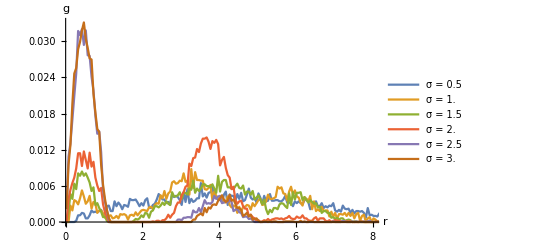

```mathematica
p1=ListPlot[gdata,Joined->True,PlotRange->{{0,8},All},AxesLabel->{Style["r",18,Italic],Style["g",18,Italic]},PlotLegends->Table["σ = "<>ToString[σs[[i]]],{i,1,Length[σs]}]]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-g-versus-r-different-σ.png",p1];
```

#### Turn on d

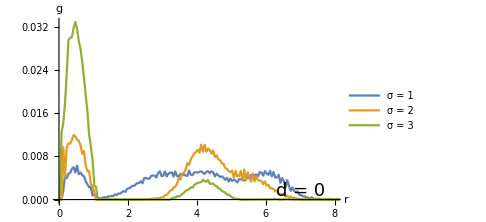
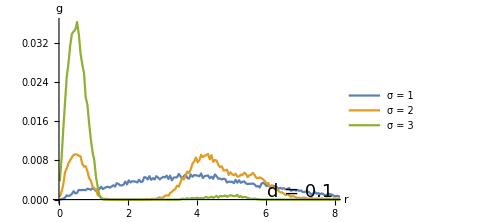
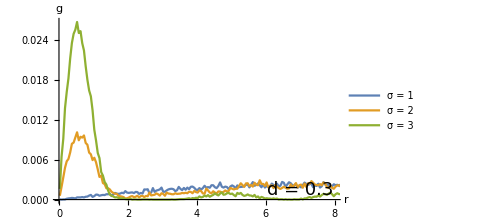
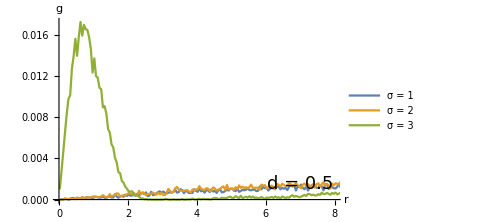

```mathematica
run[d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff,x,y,θ,xs,ys,θs},
{dt,T,n}={0.25,200,200};
{J,k}={1,1};
{R,L,Ω}={1,4,1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];{x,y,θ}=znew;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
Return[{xs,ys,θs}];
];

figs=Table[
σs=Table[σ,{σ,1,3,1}];
gdata=ParallelTable[{x,y,θ}=run[d,σ];n=Dimensions[x][[2]];t=-1;findg[x,y,θ,t,n],{σ,σs}];
ListPlot[gdata,Joined->True,ImageSize->Medium,PlotRange->{{0,8},All},AxesLabel->{Style["r",18,Italic],Style["g",18,Italic]},PlotLegends->Table["σ = "<>ToString[σs[[i]]],{i,1,Length[σs]}],Epilog->{Text[Style["d = "<>ToString[d],18],{7,0.0015}]}],
{d,{0,0.1,0.3,0.5}}
]
```

```mathematica
p1=Grid[{figs[[1;;2]],figs[[3;;4]]}]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-g-versus-r-different-σ-noise.png",p1];
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

## Analysis

### Make data

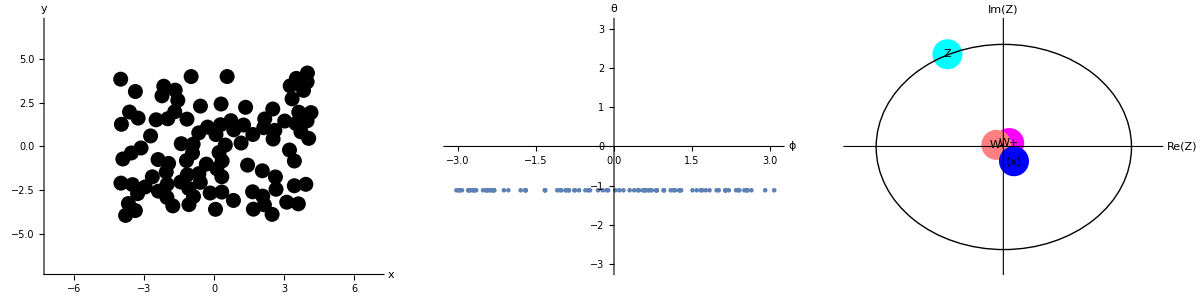

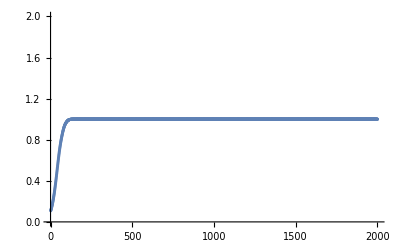

```mathematica
{dt,T,n}={0.25,500,100};
{J,k,σ}={1,1,0.5};
{R,L,d}={1,4,0};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ];
AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
plotResults[znew,7]
ListPlot[Abs[Zs]]
```

### States

### Analyze

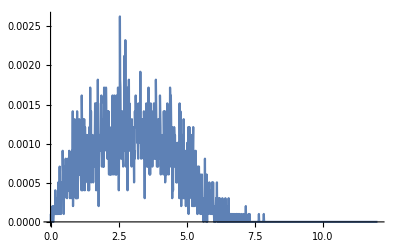

```mathematica
t=-1;
rijs=findRijNij[xs,ys,θs,t,n][[All,1]];
{min,max,dr}={0,12,0.01};
r=Table[i,{i,min,max,dr}];
r=Table[(r[[i]]+r[[i+1]])/2,{i,1,Length[r]-1}];
binnedData=BinLists[rijs,{min,max,dr}];
g=N[Table[Length[binnedData[[i]]],{i,1,Length[binnedData]}]/(n(n-1))];
ListPlot[{r,g}ᵀ,PlotRange->All,Joined->True]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{K,_Real},{σ,_Real},{ω,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,distSq,dist,xtemp,ytemp,thetatemp,vel=ConstantArray[0.0,{3,n}]},
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
thetaji=z[[3,j]]-z[[3,i]];
distSq=xji^2+yji^2;
inverseDistSq=1/distSq;
dist=√distSq;
xtemp=xji((1 + J Cos[thetaji])/dist-inverseDistSq)HeavisideTheta[σ-dist];
ytemp=yji((1 + J Cos[thetaji])/dist-inverseDistSq)HeavisideTheta[σ-dist];
thetatemp=K*Sin[thetaji] /dist; 
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=ytemp;vel[[2,j]]+=-ytemp;
vel[[3,i]]+=ω[[i]]+thetatemp;vel[[3,j]]+=ω[[j]]-thetatemp;
];
];
vel=vel/N[n];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];


(*rhs[z_,n_,J_,K_,σ_,ω_,d_]:=Block[{noise,out},
If[d>0,
noise=d*RandomVariate[NormalDistribution[0,√dt],{3,n}],
noise=Table[0.0,{i,1,3},{j,1,n}]
];
out=rhsNoiseAux[z,n,J,K,σ,ω,noise];
Return[out]
];*)

findNoise[d_,n_,dt_]:=Block[{noise},
If[d>0,
noise=RandomVariate[NormalDistribution[0,√dt],{3,n}],
noise=Table[0.0,{i,1,3},{j,1,n}]
];
Return[noise];
]

euler[z_,F_,dt_,J_,K_,σ_,ω_,d_]:=Block[{znew,n,noise},
n=Dimensions[z][[2]];
noise=findNoise[d,n,dt];
Return[z+dt F[z,n,J,K,σ,ω]+d*noise]
];

rk4[z_,F_,dt_,J_,K_,σ_,ω_,d_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,K,σ,ω,d];
k2=F[z+dt/2 k1,n,J,K,σ,ω,d];
k3=F[z+dt/2 k2,n,J,K,σ,ω,d];
k4=F[z+dt k3,n,J,K,σ,ω,d];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

plotResults[z_,L_]:=Block[{colors,p1,p2,p3,Z,Wp,Wm,meanX,meanY,ϕ,θ,L1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->15];

ϕ=ArcTan[z[[1,All]],z[[2,All]]];
θ=z[[3,All]];
p2=ListPlot[{ϕ//mod,θ//mod}ᵀ,AxesLabel->{"ϕ","θ"},LabelStyle->15,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium];

{Z,Wp,Wm}=findOrderPars[z];
{meanX,meanY}={Mean[z[[1,All]]],Mean[z[[2,All]]]};

L1=1.2;
p3=Graphics[{PointSize[0.06],
Cyan,Point[{Z//Re,Z//Im}],Black,Text["Z",{Z//Re,Z//Im}],
Magenta,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Pink,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Blue,Point[{meanX,meanY}],Black,Text["⟨x⟩",{meanX,meanY}],
Circle[{0,0},1]
},AxesOrigin->{0,0},PlotRange->{{-L1,L1},{-L1,L1}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,ImageSize->Medium];

Return[Grid[{{p1,p2,p3}}]];

];

findOrderPars[z_]:=Block[{Z,Wp,Wm,i,numOsc,ϕ,θ},
{Z,Wp,Wm}={0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
{ϕ,θ}={ArcTan[z[[1,i]],z[[2,i]]],z[[3,i]]};
Z+=Exp[ⅈ θ];
Wp+=Exp[ⅈ(ϕ+θ)];
Wm+=Exp[ⅈ(ϕ-θ)];;
];
Return[{Z/numOsc,Wp/numOsc,Wm/numOsc}]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findGamma[xs_,ys_]:=Block[{gamma,tolerance,phis,phi,s,temp,i,n},
n=Dimensions[xs][[2]];
gamma=0;
tolerance=0.05;
phis=ArcTan[xs,ys];
For[i=1,i≤n,i++,
phi=phis[[All,i]];
s=Sin[phi];
temp=(Max[s]-Min[s])/2;
If[temp>1-tolerance,gamma+=1];
];
Return[gamma/n]
];

findVelAutoCorr[xs_,ys_,n_,dt_]:=Block[{v,velAutoCorr},
velAutoCorr=Table[
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
{τ dt,Mean[Table[Normalize[v[[i,All,1]]].Normalize[v[[i,All,τ]]],{i,1,n}]]},
{τ,1,Length[xs]-1}
];
Return[velAutoCorr]
];

findV[xs_,ys_,dt_,n_]:=Block[{v},
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
Return[v]
];

findRijVijPairs[v_,xs_,ys_,t_,n_]:=Block[{dataRijVij,rij,vij,i,j},
dataRijVij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
vij=Normalize[v[[i,All,t]]].Normalize[v[[j,All,t]]];
AppendTo[dataRijVij,{rij,vij}]
]
];
dataRijVij=Sort[dataRijVij];
Return[dataRijVij]
];

findCr[xs_,ys_,dt_,n_,t_]:=Block[{v,dataRijVij,rs,vs,groupedRs,groupedVs,k,binr,binv,i,j,Cr},
v=findV[xs,ys,dt,n];
dataRijVij=findRijVijPairs[v,xs,ys,t,n];

(*Parition values*)
{rs,vs}={dataRijVij[[All,1]],dataRijVij[[All,2]]};
groupedRs=BinLists[rs,{0,3,0.05}];
groupedVs={};
k=1;
For[i=1,i≤Length[groupedRs],i++,
binr=groupedRs[[i]];
binv={};
For[j=1,j≤Length[binr],j++,
AppendTo[binv,vs[[k]]];
k+=1;
];
AppendTo[groupedVs,binv]
];

(*Find averages values*)
Cr=Table[
{Mean[groupedRs[[i]]],Mean[groupedVs[[i]]]},
{i,1,Length[groupedRs]}
];
Return[Cr]
];

findGr[xs_,ys_,n_,t_]:=Block[{i,j,rijs,rij,rs,gs,dr,rmax},
(* Find g(r) := radial density *)

(*Find pairwise rij*)
rijs={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
AppendTo[rijs,rij]
]
];

(*Radial density*)
{dr,rmax}={0.1,2};
rs=Table[i,{i,0.05,rmax,dr}];
gs=BinLists[rijs,{0,rmax,dr}];
gs=Table[Length[gs[[i]]]/(n(n-1))//N,{i,1,Length[gs]}];

Return[{rs,gs}]
];

findVelAutoCorr[xs_,ys_,dt_,NT_]:=Block[{vx,vy,v,tcutoff,c},
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
tcutoff=Round[0.5*NT];
c=Table[
{tcutoff+t*dt,Sum[Normalize[v[[i,tcutoff]]].Normalize[v[[i,t]]],{i,1,n}]/n},
{t,tcutoff,NT-1}
];
Return[c]
];

findRijNij[xs_,ys_,θs_,t_,n_]:=Block[{dataRijNij,rij,nij,i,j},
dataRijNij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
nij={Cos[θs[[t,i]]],Sin[θs[[t,i]]]}.{Cos[θs[[t,j]]],Sin[θs[[t,j]]]};
AppendTo[dataRijNij,{rij,nij}]
]
];
dataRijNij=Sort[dataRijNij];
Return[dataRijNij]
];

clean[data_]:=Block[{cleanData,element,condition},
cleanData={};
For[i=1,i≤Length[data],i++,
element=data[[i]];
condition=NumberQ[element[[1]]]&&NumberQ[element[[2]]];
If[condition,AppendTo[cleanData,element]]
];
Return[cleanData]
]

findCthetathetaR[xs_,ys_,θs_,t_,n_]:=Block[{data,dr,rmax,binnedData,meanBinnedData,RijNijpairs},
RijNijpairs=findRijNij[xs,ys,θs,t,n]; (**)
dr=0.1;
rmax=Ceiling[Max[RijNijpairs[[All,1]]]]+1;
binnedData=BinLists[RijNijpairs,{0,rmax,dr},{-1,1,2}];
meanBinnedData=Table[{binnedData[[i,1]][[All,1]]//Mean,binnedData[[i,1]][[All,2]]//Mean},{i,1,Length[binnedData]}];
(*meanBinnedData=clean[meanBinnedData];*)
Return[{RijNijpairs,meanBinnedData}]
];

run1[σ_,d_]:=Block[{dt,T,n,J,k,R,L,ω,z0,znew,t,NT,xs,ys,θs,x,y,θ},
{dt,T,n}={0.25,200,300};
{J,k}={1,1};
{R,L}={1,5};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];{x,y,θ}=znew;
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ];
];
Return[{znew,xs,ys,θs}];
];
```